## Fig 1:

## Initializations for BB1 plot:

```mathematica
Clear[a,θ]
a=Cos[θ/2]
w[a_]:={{a,I*√(1-a^2)},{I*√(1-a^2),a}}
ϕ={π/2,-η,2*η,0,-2*η,η}
Z = {{1,0},{0,-1}};                                                   
U = (Cos[ϕ[[1]]]*Id+I*Sin[ϕ[[1]]]*Z).(∏_(k=2)^6 (w[a].(Cos[ϕ[[k]]]*Id+I*Sin[ϕ[[k]]]*Z)))//Simplify
```

Cos[θ/2]

{π/2,-0.911738,1.82348,0,-1.82348,0.911738}

{{(0.+1. ⅈ) Cos[θ/2]^5,-0.176777 (1-Cos[θ])^(5/2)},{0.176777 (1-Cos[θ])^(5/2),(0.-1. ⅈ) Cos[θ/2]^5}}

## Writing Eq. 3 explicitly for BB1:

```mathematica
η=0.5*ArcCos[-0.25];
Id={{1,0},{0,1}};
U1=(Cos[ϕ[[1]]]*Id+I*Sin[ϕ[[1]]]*Z).w[a].(Cos[ϕ[[2]]]*Id+I*Sin[ϕ[[2]]]*Z).w[a].(Cos[ϕ[[3]]]*Id+I*Sin[ϕ[[3]]]*Z).w[a].(Cos[ϕ[[4]]]*Id+I*Sin[ϕ[[4]]]*Z).w[a].(Cos[ϕ[[5]]]*Id+I*Sin[ϕ[[5]]]*Z).w[a].(Cos[ϕ[[6]]]*Id+I*Sin[ϕ[[6]]]*Z) //Simplify
```

{{(-0.484123+1.875 ⅈ) Cos[θ/2]+(0.968246-1.25 ⅈ) Cos[θ/2]^3-(0.484123-0.375 ⅈ) Cos[θ/2]^5,((-1.+2.77556×10^-16 ⅈ)+(1.375-0.484123 ⅈ) Cos[θ/2]^2-(0.375-0.484123 ⅈ) Cos[θ/2]^4) √(Sin[θ/2]^2)},{((1.+2.77556×10^-16 ⅈ)-(1.375+0.484123 ⅈ) Cos[θ/2]^2+(0.375+0.484123 ⅈ) Cos[θ/2]^4) √(Sin[θ/2]^2),(-0.484123-1.875 ⅈ) Cos[θ/2]+(0.968246+1.25 ⅈ) Cos[θ/2]^3-(0.484123+0.375 ⅈ) Cos[θ/2]^5}}

## The plot:

```mathematica
pf=ComplexExpand[Abs[p1]];
```

```mathematica
p1=({{1,0}}.U1.{{1},{0}})
```

{{(-0.484123+1.875 ⅈ) Cos[θ/2]+(0.968246-1.25 ⅈ) Cos[θ/2]^3-(0.484123-0.375 ⅈ) Cos[θ/2]^5}}

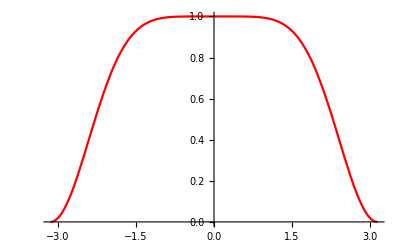

```mathematica
pl1=Plot[pf^2,{θ,-π,π},PlotStyle->Red]
```

## Plotting the trivial case [ϕ = (0,0)]:

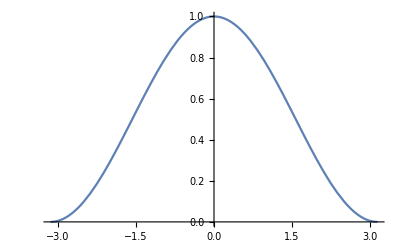

```mathematica
ϕ1={0,0};
U2=(Cos[ϕ1[[1]]]*Id+I*Sin[ϕ1[[1]]]*Z).w[a].(Cos[ϕ1[[2]]]*Id+I*Sin[ϕ1[[2]]]*Z);
p2=({{1,0}}.U2.{{1},{0}});
pf2=ComplexExpand[Abs[p2]];
pf2^2;
pl2=Plot[pf2^2,{θ,-π,π}]
```

## Merging two plots to get Fig. 1

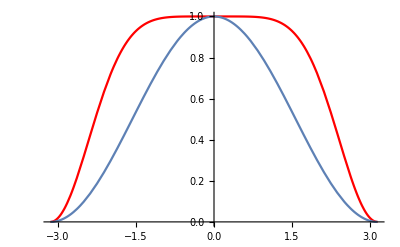

```mathematica
Show[pl1,pl2,PlotLegends->{"BB1","Trivial"}]
```

```mathematica
d=input["Enter"]
```

input[Enter]

```mathematica
P[d_,a_]:=ChebyshevT[d,a] 
Q[a_]:=ChebyshevT[d-1,a]
```

```mathematica
P[10,a=Cos[θ]]
```

-1+50 Cos[θ]^2-400 Cos[θ]^4+1120 Cos[θ]^6-1280 Cos[θ]^8+512 Cos[θ]^10

## Fig 20:

## Phase sequence  from D1, D2, D3 (Fig 20):

```mathematica
ϕ1={-1.58023603,-1.55147987,-1.6009483,-1.52812171,-1.62884337,-1.49242141,-1.67885248,-1.41255145,-1.8386054,-0.87463828,-0.87463828,-1.8386054,-1.41255145,-1.67885248,-1.49242141,-1.62884337,-1.52812171,-1.6009483,-1.55147987,-1.58023603}
```

{-1.58024,-1.55148,-1.60095,-1.52812,-1.62884,-1.49242,-1.67885,-1.41255,-1.83861,-0.874638,-0.874638,-1.83861,-1.41255,-1.67885,-1.49242,-1.62884,-1.52812,-1.60095,-1.55148,-1.58024}

```mathematica
w[a1_]:={{a1,I*√(1-a1^2)},{I*√(1-a1^2),a1}}
w[a1]
```

{{a1,ⅈ √(1-a1^2)},{ⅈ √(1-a1^2),a1}}

```mathematica
U3=(Cos[ϕ1[[1]]]*Id+I*Sin[ϕ1[[1]]]*Z).w[a1].(Cos[ϕ1[[2]]]*Id+I*Sin[ϕ1[[2]]]*Z).w[a1].(Cos[ϕ1[[3]]]*Id+I*Sin[ϕ1[[3]]]*Z).w[a1].(Cos[ϕ1[[4]]]*Id+I*Sin[ϕ1[[4]]]*Z).w[a1].(Cos[ϕ1[[5]]]*Id+I*Sin[ϕ1[[5]]]*Z).w[a1].(Cos[ϕ1[[6]]]*Id+I*Sin[ϕ1[[6]]]*Z).w[a1].(Cos[ϕ1[[7]]]*Id+I*Sin[ϕ1[[7]]]*Z).w[a1].(Cos[ϕ1[[8]]]*Id+I*Sin[ϕ1[[8]]]*Z).w[a1].(Cos[ϕ1[[9]]]*Id+I*Sin[ϕ1[[9]]]*Z).w[a1].(Cos[ϕ1[[10]]]*Id+I*Sin[ϕ1[[10]]]*Z).w[a1].(Cos[ϕ1[[11]]]*Id+I*Sin[ϕ1[[11]]]*Z).w[a1].(Cos[ϕ1[[12]]]*Id+I*Sin[ϕ1[[12]]]*Z).w[a1].(Cos[ϕ1[[13]]]*Id+I*Sin[ϕ1[[13]]]*Z).w[a1].(Cos[ϕ1[[14]]]*Id+I*Sin[ϕ1[[14]]]*Z).w[a1].(Cos[ϕ1[[15]]]*Id+I*Sin[ϕ1[[15]]]*Z).w[a1].(Cos[ϕ1[[16]]]*Id+I*Sin[ϕ1[[16]]]*Z).w[a1].(Cos[ϕ1[[17]]]*Id+I*Sin[ϕ1[[17]]]*Z).w[a1].(Cos[ϕ1[[18]]]*Id+I*Sin[ϕ1[[18]]]*Z).w[a1].(Cos[ϕ1[[19]]]*Id+I*Sin[ϕ1[[19]]]*Z).w[a1].(Cos[ϕ1[[20]]]*Id+I*Sin[ϕ1[[20]]]*Z) //Simplify
```

{{(1.65739-0.845438 ⅈ) a1-(0.0179417-0.974081 ⅈ) a1^3-(0.857359-0.650264 ⅈ) a1^5-(0.259413-0.0812614 ⅈ) a1^7-(0.0181459-0.00345403 ⅈ) a1^9-(0.000487334-0.000059474 ⅈ) a1^11-(5.3581×10^-6-4.38025×10^-7 ⅈ) a1^13-(2.52501×10^-8-1.35696×10^-9 ⅈ) a1^15-(4.58596×10^-11-1.56816×10^-12 ⅈ) a1^17-(2.77336×10^-14-5.57354×10^-16 ⅈ) a1^19,√(1-a1^2) ((1.08908×10^-16-1. ⅈ)-(5.0578×10^-17-1.23085 ⅈ) a1^2-(1.37339×10^-15-1.13509 ⅈ) a1^4+(5.88722×10^-15+0.278559 ⅈ) a1^6-(2.20299×10^-14-0.0186537 ⅈ) a1^8+(3.35382×10^-14+0.000493026 ⅈ) a1^10-(3.20991×10^-14-5.38547×10^-6 ⅈ) a1^12+(2.41694×10^-14+2.53033×10^-8 ⅈ) a1^14-(5.61876×10^-15-4.59364×10^-11 ⅈ) a1^16+(5.86101×10^-18+2.77251×10^-14 ⅈ) a1^18)},{√(1-a1^2) ((-1.08908×10^-16-1. ⅈ)+(5.0578×10^-17+1.23085 ⅈ) a1^2+(1.37339×10^-15+1.13509 ⅈ) a1^4-(5.88722×10^-15-0.278559 ⅈ) a1^6+(2.20299×10^-14+0.0186537 ⅈ) a1^8-(3.35382×10^-14-0.000493026 ⅈ) a1^10+(3.20991×10^-14+5.38547×10^-6 ⅈ) a1^12-(2.41694×10^-14-2.53033×10^-8 ⅈ) a1^14+(5.61876×10^-15+4.59364×10^-11 ⅈ) a1^16-(5.86101×10^-18-2.77251×10^-14 ⅈ) a1^18),(1.65739+0.845438 ⅈ) a1-(0.0179417+0.974081 ⅈ) a1^3-(0.857359+0.650264 ⅈ) a1^5-(0.259413+0.0812614 ⅈ) a1^7-(0.0181459+0.00345403 ⅈ) a1^9-(0.000487334+0.000059474 ⅈ) a1^11-(5.3581×10^-6+4.38025×10^-7 ⅈ) a1^13-(2.52501×10^-8+1.35696×10^-9 ⅈ) a1^15-(4.58596×10^-11+1.56816×10^-12 ⅈ) a1^17-(2.77336×10^-14+5.57354×10^-16 ⅈ) a1^19}}

## Plot Fig 20:

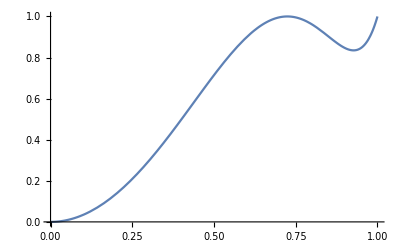

```mathematica
p3=({{1,0}}.U3.{{1},{0}});
pf3=ComplexExpand[Abs[p3]];
pl3=Plot[pf3^2,{a1,0,1}]
```

```mathematica
b={{2,3},{3,2}};
s={{3,0},{0,3}};
(∏_(k=1)^1 (s.b)).(∏_(k=1)^1 (s.b))
```

{{117,108},{108,117}}

```mathematica
n=2;
s={{1,2},{2,1}};
b={{1,2},{2,1}};
result=s.b;
Do[result=result.s.b,{i,1,n}];
result
```

{{365,364},{364,365}}